```mathematica
y0=1.2
y1=1.4
y2=1.95
y3=2.23
y4=2
y5=2.4
y6=2.1
```

1.2

1.4

1.95

2.23

2

2.4

2.1

```mathematica
x0=0.8
x1=1.2
x2=1.7
x3=2.3
x4=2.5
x5=3.0
x6=4.1
```

0.8

1.2

1.7

2.3

2.5

3.

4.1

```mathematica
h0=x1-x0
h1=x2-x1
h2=x3-x2
h3=x4-x3
h4=x5-x4
h5=x6-x5
```

0.4

0.5

0.6

0.2

0.5

1.1

```mathematica
Clear[c0,c1,c2,c3,c4,c5,c6]
```

```mathematica
Solve[{c0==0,h0 c0+2(h0+h1) c1+h1 c2==3/h1(y2-y1)-3/h0(y1-y0),h1 c1+2(h1+h2)c2+h2 c3==3/h2(y3-y2)-3/h1(y2-y1),h2 c2+2(h2+h3)c3+h3 c4==3/h3(y4-y3)-3/h2(y3-y2),h3 c3+2(h3+h4)c4+h4 c5==3/h4(y5-y4)-3/h3(y4-y3),h4 c4+2(h4+h5)c5+h5 c6==3/h5(y6-y5)-3/h4(y5-y4),c6==0}]
```

{{c0→0.,c1→1.02711,c2→-0.0976084,c3→-3.6647,c4→5.3604,c5→-1.84324,c6→0.}}

```mathematica
c0=0
c1=1.02711
c2=-0.0976084
c3=-3.6647
c4=5.3604
c5=-1.84324
c6=0
```

0

1.02711

-0.0976084

-3.6647

5.3604

-1.84324

0

```mathematica
a0=y0
a1=y1
a2=y2
a3=y3
a4=y4
a5=y5
```

1.2

1.4

1.95

2.23

2

2.4

```mathematica
d0=(c1-c0)/(3h0)
d1=(c2-c1)/(3h1)
d2=(c3-c2)/(3h2)
d3=(c4-c3)/(3h3)
d4=(c5-c4)/(3h4)
d5=(c6-c5)/(3h5)
```

0.855925

-0.749812

-1.98172

15.0418

-4.80243

0.558558

```mathematica
b0=1/h0*(y1-y0)-h0/3*(2c0+c1)
b1=1/h1*(y2-y1)-h1/3*(2c1+c2)
b2=1/h2*(y3-y2)-h2/3*(2c2+c3)
b3=1/h3*(y4-y3)-h3/3*(2c3+c4)
b4=1/h4*(y5-y4)-h4/3*(2c4+c5)
b5=1/h5*(y6-y5)-h5/3*(2c5+c6)
```

0.363052

0.773898

1.23865

-1.01873

-0.679593

1.07898

```mathematica
x5
a5
b5
c5
d5
```

3.

2.4

1.07898

-1.84324

0.558558

```mathematica
S0[x_]:=a0+b0(x-x0)+c0(x-x0)^2+d0(x-x0)^3
S1[x_]:=a1+b1(x-x1)+c1(x-x1)^2+d1(x-x1)^3
S2[x_]:=a2+b2(x-x2)+c2(x-x2)^2+d2(x-x2)^3
S3[x_]:=a3+b3(x-x3)+c3(x-x3)^2+d3(x-x3)^3
S4[x_]:=a4+b4(x-x4)+c4(x-x4)^2+d4(x-x4)^3
S5[x_]:=a5+b5(x-x5)+c5(x-x5)^2+d5(x-x5)^3
```

```mathematica
Expand[S0[x]]
Expand[S1[x]]
Expand[S2[x]]
Expand[S3[x]]
Expand[S4[x]]
Expand[S5[x]]
```

0.471325+2.00643 x-2.05422 x^2+0.855925 x^3

3.24604-4.93035 x+3.72643 x^2-0.749812 x^3

9.29839-15.611 x+10.0092 x^2-1.98172 x^3

-197.827+254.553 x-107.453 x^2+15.0418 x^3

112.239-117.527 x+41.3786 x^2-4.80243 x^3

-32.5072+27.2195 x-6.87026 x^2+0.558558 x^3

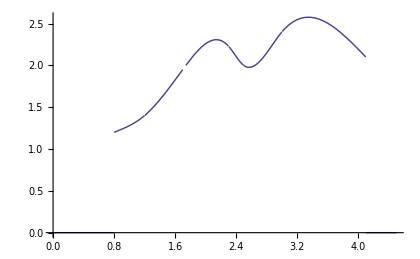

```mathematica
Plot[Piecewise[{{S0[x],0.8≤ x≤1.2},{S1[x],1.2≤ x≤1.7},{S2[x],1.7≤ x≤2.3},{S3[x],2.3≤ x≤2.5},{S4[x],2.5≤ x≤3.},{S5[x],3.≤ x≤4.1}}],{x,0,4.5}]
```